### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,Y} ∈Reals && τ >1&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,Y}]]]
```

(τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/(2 (1+Y) (1+τ^2)^2)

### Compute total mass

```mathematica
mtot = FullSimplify[Assuming[{τ,Y} ∈Reals && τ >1&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2)),{x,0,Infinity}]]]
```

(τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2)

### Plot the 2 cases for an examples

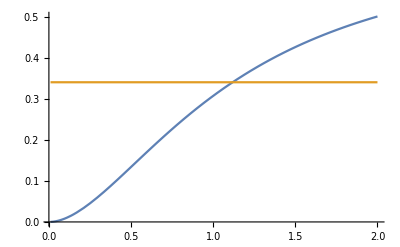

```mathematica
Plot[{2*mhalf/.τ->1.2,mtot/.τ->1.2},{Y,.01,2},PlotRange->Full]
```

### Ok they intersect, find solution numerically

```mathematica
tauSol[Y_]:=FindRoot[1/(1+Y)(-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])==(-1+(π-τ) τ+(-1+τ^2) Log[τ]),{τ,Y^1.7}]
```

### Make a table of solutions

```mathematica
τTab = Table[{Y,tauSol[Y][[1,2]]},{Y,0.01,2,0.01}];
```

### Plot it

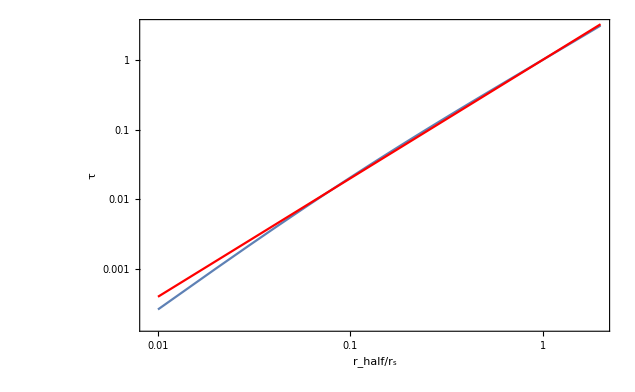

```mathematica
Show[ListLogLogPlot[τTab,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[x^1.7,{x,0.01,2},PlotStyle->Red]]
```

### Save to file

```mathematica
Export["tau_vs_xhalf.dat",τTab,"Data"]
```

tau_vs_xhalf.dat

### For fun, let’s try to derive the 2.1626 for NFW

```mathematica
FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Difvmax = D[1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2]),X]]]
```

(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))

```mathematica
Series[Difvmax,{τ,Infinity,2}]
```

(X+2 X^2-Log[1+X]-2 X Log[1+X]-X^2 Log[1+X])/(X^2 (1+X)^2)+(-6 X-9 X^2-2 X^3-X^4+6 Log[1+X]+12 X Log[1+X]+6 X^2 Log[1+X])/(2 X^2 (1+X)^2 τ^2)+O[1/τ]^3

Solve for the leading term in the derivative is zero (corresponding to v_max)

```mathematica
FindRoot[(X+2 X^2-Log[1+X]-2 X Log[1+X]-X^2 Log[1+X])/(X^2 (1+X)^2)==0,{X,2}]
```

{X→2.16258}

Victory!

### Study effect of τ

```mathematica
Tabtau[τh_]:= FindRoot[Difvmax/.τ-> τh,{X,0.005}]
```

### Make a table of solutions

```mathematica
XmaxTab = Table[{τ,Tabtau[τ][[1,2]]},{τ,.001,2,0.001}];
```

### Plot it

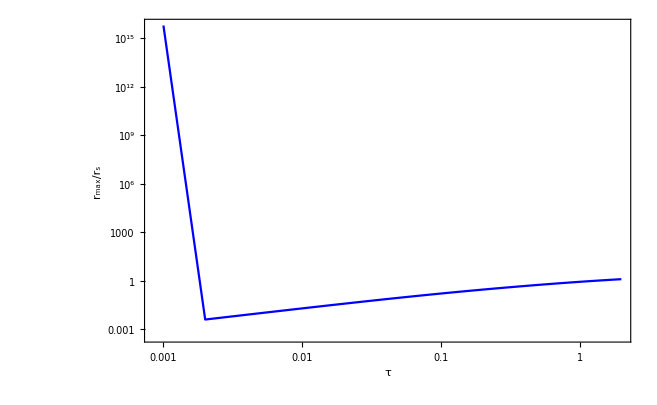

```mathematica
ListLogLogPlot[{XmaxTab},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, s]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue,Red}]
```

```mathematica
tautab = Table[{XmaxTab[[i,2]],XmaxTab[[i,1]]},{i,2,Length[XmaxTab]}];
```

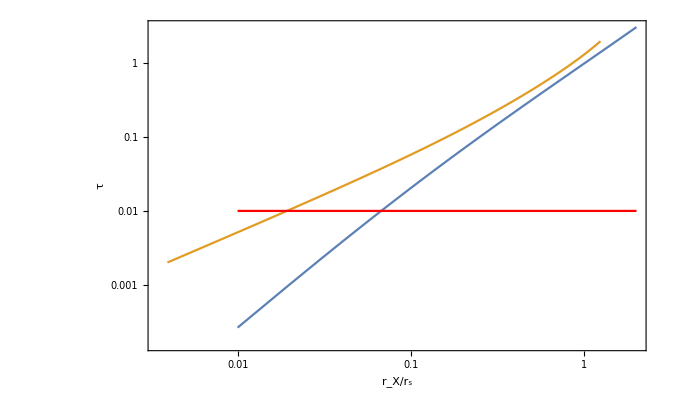

```mathematica
Show[ListLogLogPlot[{τTab,tautab },Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[0.01,{x,0.01,2},PlotStyle->Red]]
```

```mathematica
1/0.8503555895558775
```

1.17598

### Save to file

```mathematica
Export["xmax_vs_tau.dat",XmaxTab,"Data"]
```

xmax_vs_tau.dat

## Try solving both at the same time

```mathematica
Sol[rh_,rmax_,τs_,rss_]:=FindRoot[{(1/(1+Y) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])/. Y-> rh/rs)/(-1+(π-τ) τ+(-1+τ^2) Log[τ])==1,(((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))/.X-> rmax/rs)==0},{{τ,τs,0,2},{rs,rss,rmax/2.16258,15*rmax}}, MaxIterations->1000,AccuracyGoal->8]
```

1.14745

0.14934

{τ→0.908999,rs→0.169137}

{τ→0.88419}

0.799352

0.492566

0.000584363

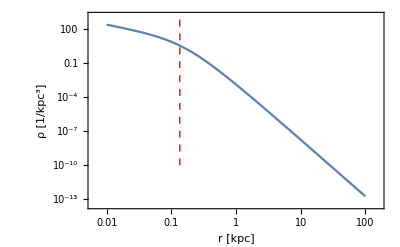

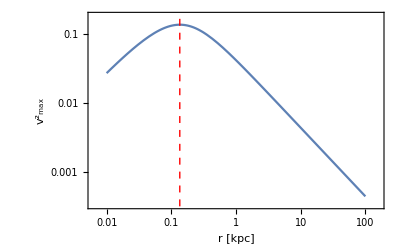

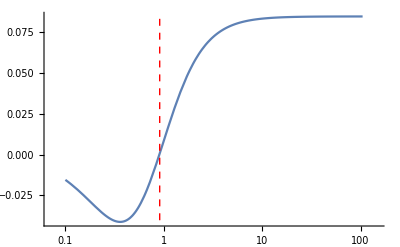

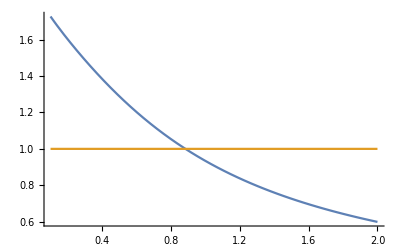

```mathematica
rmax =.1352;
α=1.16;
rh=α*rmax;
0.35 α^8
rmax/(0.5 α^4)
Solh=Sol[rh,rmax,0.35 α^8,rmax/(0.5 α^4)]
Solτ=tauSol[rh/rs]/.Solh[[2]]
Xsol=rmax/rs/.Solh[[2]]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
line2=Line[{{Log[Solh[[1,2]]],-0.3},{Log[Solh[[1,2]]],0.3}}];
(1/(2 (1+Y) (1+τ^2)^2)τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/((τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2))/.Y-> rh/rs/.Solh 
(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))/.X-> rmax/rs/.Solh 
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.Solh },{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"},Epilog->{Directive[lineStyle],line1}]
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
LogLinearPlot[{(τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2))/.X->Xsol},{τ,0.1,105},Epilog->{Directive[lineStyle],line2}]
Plot[{(1/((1+Y) (1+τ^2)^2)τ^2 (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2]))/((τ^2 (-1+(π-τ) τ+(-1+τ^2) Log[τ]))/((1+τ^2)^2))/.Y-> rh/rs/.Solh[[2]],1},{τ,0.1,2} ]
```

```mathematica
rmax=1.234;
TabαSol = ParallelTable[SolT = Sol[α rmax,rmax,If[α<1.5,0.9 α^4,2.7 α^1.9]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,1.2,28,0.02}];
```

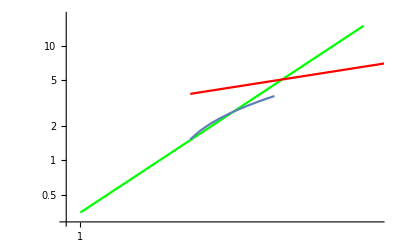

```mathematica
Show[LogLogPlot[{.35 x^8},{x,1,1.6},PlotStyle->{Green}],ListLogLogPlot[TabαSol[[1;;10,{1,2}]],Joined->True],LogLogPlot[{2.7 x^1.9},{x,1.2,28},PlotStyle->{Red}]]
```

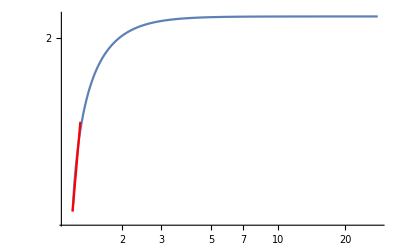

```mathematica
Show[ListLogLogPlot[TabαSol[[1;;,{1,3}]],Joined->True,PlotRange->Full],LogLogPlot[0.52 x^4,{x,1.2,1.3},PlotStyle->Red]]
```

```mathematica
Export["tau_xmax_vs_rhormax.dat",TabαSol,"Data"]
```

tau_xmax_vs_rhormax.dat

```mathematica
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
```

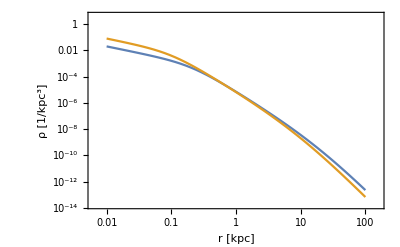

```mathematica
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.τ-> 0.01/.rs-> 20,1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.τ-> 0.01/.rs-> 10},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"}]
```

## Instead of finding actual solution, find closest tNFW halos that fit

```mathematica
Solclose2[rh_,rmax_]:=NMinimize[{((1/(1+Y) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])-(-1+(π-τ) τ+(-1+τ^2) Log[τ]))^2 + ((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))^2)/. Y-> rh/rs /.X-> rmax/rs,τ>0, rs>rmax/2.16258},{τ,rs}, MaxIterations->1000,AccuracyGoal->8]
```

{2.66538×10^-6,{τ→0.898206,rs→1.52931}}

x_max= 0.806898

M_(1/2) = 0.499888

dv_max^2/dr(r_max) = -0.00161607

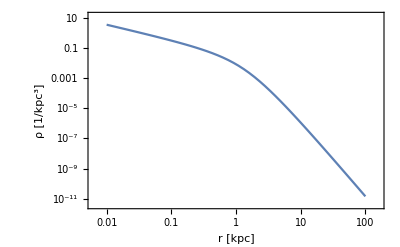

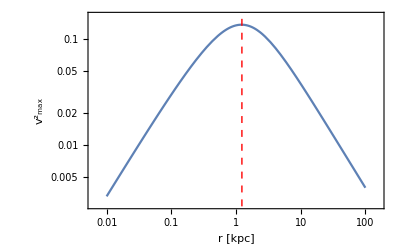

```mathematica
rmax =1.234;
α=1.16;
rh=α*rmax;
 Solh2 = Solclose2[rh,rmax]
Print["x_max= ", rmax/rs/. Solh2[[2]]]
Print["M_(1/2) = ",(1/(2(1+Y)) (-2 Y (1+τ^2)+4 (1+Y) τ ArcTan[Y/τ]+2 (1+Y) (-1+τ^2) Log[(1+Y) τ]-(1+Y) (-1+τ^2) Log[Y^2+τ^2])/. Y-> rh/rs)/(-1+(π-τ) τ+(-1+τ^2) Log[τ])/.Y-> rh/rs/.Solh2[[2]]]

Print["dv_max^2/dr(r_max) = ",(((τ^2 (2 X (1+τ^2) (X+X^2+X^3+τ^2+2 X τ^2)-(1+X)^2 (X^2+τ^2) (4 τ ArcTan[X/τ]+(-1+τ^2) (2 Log[(1+X) τ]-Log[X^2+τ^2]))))/(2 X^2 (1+X)^2 (1+τ^2)^2 (X^2+τ^2)))/.X-> rmax/rs)/.Solh2[[2]]]
LogLogPlot[{1/(4π rs^3)1/(x(1+x)^2)(τ^2/(τ^2+x^2))/.x-> r/rs/.Solh2[[2]]},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","ρ [1/kpc^3]"}]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
LogLogPlot[{1/X 1/(2 (1+X) (1+τ^2)^2)τ^2 (-2 X (1+τ^2)+4 (1+X) τ ArcTan[X/τ]+2 (1+X) (-1+τ^2) Log[(1+X) τ]-(1+X) (-1+τ^2) Log[X^2+τ^2])/.X-> r/rs/.Solh2[[2]]},{r,0.01,100},Frame->True, FrameLabel->{"r [kpc]","(v^2)_max "},Epilog->{Directive[lineStyle],line1}]
```

### Tabulate approximate solution

```mathematica
rmax=1.234;
TabαSolapprox = ParallelTable[SolT =Solclose2[α rmax,rmax][[2]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,0.55,1.17,0.005}];
```

```mathematica
rmax=1.234;
TabαSolapprox2 = ParallelTable[SolT =Solclose2[α rmax,rmax][[2]];{α,SolT[[1,2]],rmax/SolT[[2,2]]},{α,1.16,1.18,0.001}];
```

```mathematica
TabαSolapprox
```

{{0.55,1.3268,2.16258},{0.555,1.34656,2.16258},{0.56,1.36642,2.16258},{0.565,1.3864,2.16258},{0.57,1.40649,2.16258},{0.575,1.42669,2.16258},{0.58,1.447,2.16258},{0.585,1.46742,2.16258},{0.59,1.48796,2.16258},{0.595,1.5086,2.16258},{0.6,1.52935,2.16258},{0.605,1.55021,2.16258},{0.61,1.57119,2.16258},{0.615,1.59227,2.16258},{0.62,1.61346,2.16258},{0.625,1.63476,2.16258},{0.63,1.65617,2.16258},{0.635,1.67769,2.16258},{0.64,1.69932,2.16258},{0.645,1.72105,2.16258},{0.65,1.7429,2.16258},{0.655,1.76485,2.16258},{0.66,1.78691,2.16258},{0.665,1.80909,2.16258},{0.67,1.83136,2.16258},{0.675,1.85375,2.16258},{0.68,1.87624,2.16258},{0.685,1.89884,2.16258},{0.69,1.92155,2.16258},{0.695,1.94437,2.16258},{0.7,1.96729,2.16258},{0.705,1.99032,2.16258},{0.71,2.01346,2.16258},{0.715,2.0367,2.16258},{0.72,2.06006,2.16258},{0.725,2.08351,2.16258},{0.73,2.10708,2.16258},{0.735,2.13075,2.16258},{0.74,2.15453,2.16258},{0.745,2.17841,2.16258},{0.75,2.2024,2.16258},{0.755,2.22649,2.16258},{0.76,2.2507,2.16258},{0.765,2.275,2.16258},{0.77,2.29941,2.16258},{0.775,2.32393,2.16258},{0.78,2.34855,2.16258},{0.785,2.37328,2.16258},{0.79,2.39811,2.16258},{0.795,2.42305,2.16258},{0.8,2.44809,2.16258},{0.805,2.47323,2.16258},{0.81,2.49848,2.16258},{0.815,2.52384,2.16258},{0.82,2.5493,2.16258},{0.825,2.57486,2.16258},{0.83,2.60053,2.16258},{0.835,2.6263,2.16258},{0.84,2.65217,2.16258},{0.845,2.67815,2.16258},{0.85,2.70423,2.16258},{0.855,2.73041,2.16258},{0.86,2.7567,2.16258},{0.865,2.78309,2.16258},{0.87,2.80958,2.16258},{0.875,2.83617,2.16258},{0.88,2.86287,2.16258},{0.885,2.88967,2.16258},{0.89,2.91657,2.16258},{0.895,2.94358,2.16258},{0.9,2.97068,2.16258},{0.905,2.99789,2.16258},{0.91,3.0252,2.16258},{0.915,3.05262,2.16258},{0.92,3.08013,2.16258},{0.925,3.10774,2.16258},{0.93,3.13546,2.16258},{0.935,3.16328,2.16258},{0.94,3.1912,2.16258},{0.945,3.21922,2.16258},{0.95,3.24734,2.16258},{0.955,3.27557,2.16258},{0.96,3.30389,2.16258},{0.965,3.33231,2.16258},{0.97,3.36084,2.16258},{0.975,3.38947,2.16258},{0.98,3.41819,2.16258},{0.985,3.44702,2.16258},{0.99,3.47594,2.16258},{0.995,3.50497,2.16258},{1.,3.5341,2.16258},{1.005,2.35339,1.68053},{1.01,1.94971,1.49056},{1.015,1.78006,1.40279},{1.02,1.66294,1.33887},{1.025,1.57176,1.28702},{1.03,1.49916,1.24411},{1.035,1.43736,1.20649},{1.04,1.38429,1.17325},{1.045,1.33788,1.14341},{1.05,1.29684,1.11638},{1.055,1.26015,1.09165},{1.06,1.22709,1.06888},{1.065,1.1971,1.0478},{1.07,1.16969,1.02816},{1.075,1.1446,1.00982},{1.08,1.12145,0.992606},{1.085,1.10002,0.976394},{1.09,1.08012,0.961084},{1.095,1.06157,0.946581},{1.1,1.04424,0.932814},{1.105,1.028,0.919713},{1.11,1.01273,0.907221},{1.115,0.998357,0.895285},{1.12,0.984739,0.883836},{1.125,0.971953,0.872911},{1.13,0.959791,0.862397},{1.135,0.948246,0.852287},{1.14,0.937268,0.842553},{1.145,0.926813,0.833169},{1.15,0.916895,0.824143},{1.155,0.907434,0.815427},{1.16,0.898185,0.806886},{1.165,0.889482,0.798703},{1.17,0.881118,0.790762}}

```mathematica
TabαSolapprox2
```

{{1.16,0.898206,0.806898},{1.161,0.89811,0.806164},{1.162,0.894715,0.803612},{1.163,0.892927,0.80195},{1.164,0.893337,0.801502},{1.165,0.889483,0.798703},{1.166,0.887877,0.797148},{1.167,0.890529,0.797942},{1.168,0.886555,0.795085},{1.169,0.886506,0.794393},{1.17,0.889904,0.795595},{1.171,0.879631,0.789283},{1.172,0.891949,0.795386},{1.173,0.888149,0.792643},{1.174,0.874669,0.784582},{1.175,0.941676,0.820248},{1.176,1.00127,0.851002},{1.177,1.04297,0.871839},{1.178,1.07798,0.88893},{1.179,1.10863,0.903588},{1.18,1.13602,0.916446}}

```mathematica
Export["tau_xmax_vs_rhormax_low.dat",TabαSolapprox,"Data"]
```

tau_xmax_vs_rhormax_low.dat

```mathematica
Export["tau_xmax_vs_rhormax_mid.dat",TabαSolapprox2 ,"Data"]
```

tau_xmax_vs_rhormax_mid.dat

## Change the truncation behavior to a steeper one

### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,Y} ∈Reals && τ >0&&Y>0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2))^2,{x,0,Y}]]];
```

### Compute total mass

```mathematica
mtot = FullSimplify[Assuming[τ ∈Reals && τ >0,Integrate[x/(1+x)^2(τ^2/(τ^2+x^2))^2,{x,0,Infinity}]]];
```

### Plot the 2 cases for an examples

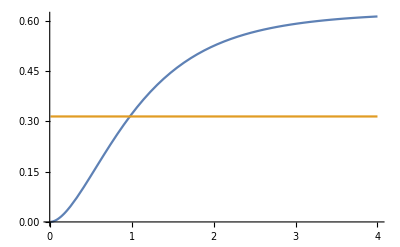

```mathematica
Plot[{2*mhalf/.τ-> 2,mtot/.τ-> 2},{Y,.01,4},PlotRange->Full]
```

#### Solve for the solution

```mathematica
tauSol[Y_]:=FindRoot[2 mhalf==mtot,{τ,3 Y^1.2}]
```

### Make a table of solutions

```mathematica
τTab = Table[{Y,tauSol[Y][[1,2]]},{Y,0.001,2,0.001}];
```

### Plot it

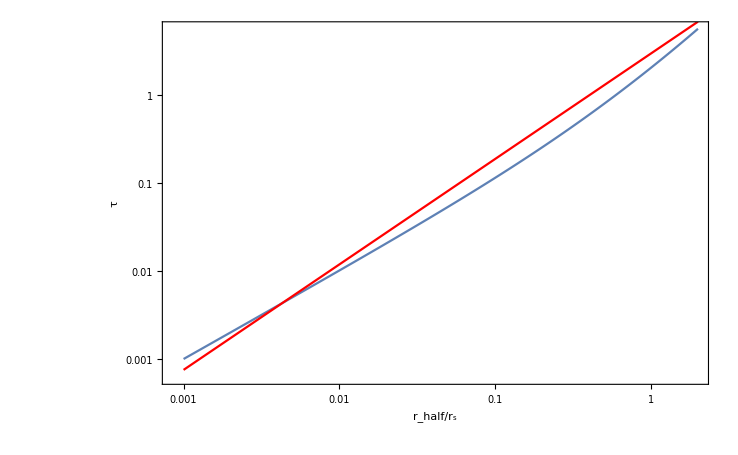

```mathematica
Show[ListLogLogPlot[τTab,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[3 x^1.2,{x,0.001,2},PlotStyle->Red]]
```

#### Now handle vmax

```mathematica
FullSimplify[Assuming[{Y,τ} ∈Reals && Y>0 && τ>0,Difvmax = D[1/Y mhalf,Y]]];
```

```mathematica
Tabtau[τh_]:= FindRoot[Difvmax/.τ-> τh,{Y,0.9τh}]
```

### Make a table of solutions

```mathematica
XmaxTab = Table[{τ,Tabtau[τ][[1,2]]},{τ,.001,1,0.001}];
```

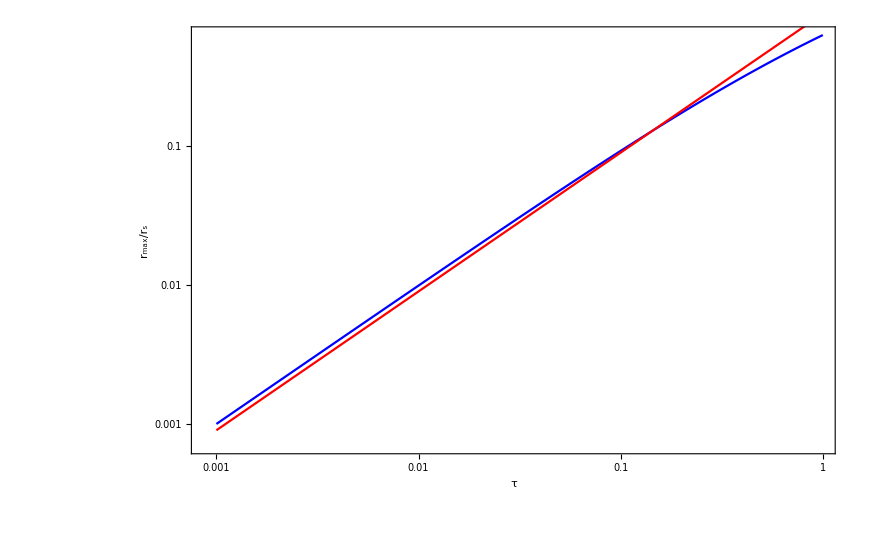

```mathematica
Show[ListLogLogPlot[{XmaxTab},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, s]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue,Red}],LogLogPlot[0.9x,{x,0.001,1},PlotStyle->Red]]
```

```mathematica
tautab = Table[{XmaxTab[[i,2]],XmaxTab[[i,1]]},{i,2,Length[XmaxTab]}];
```

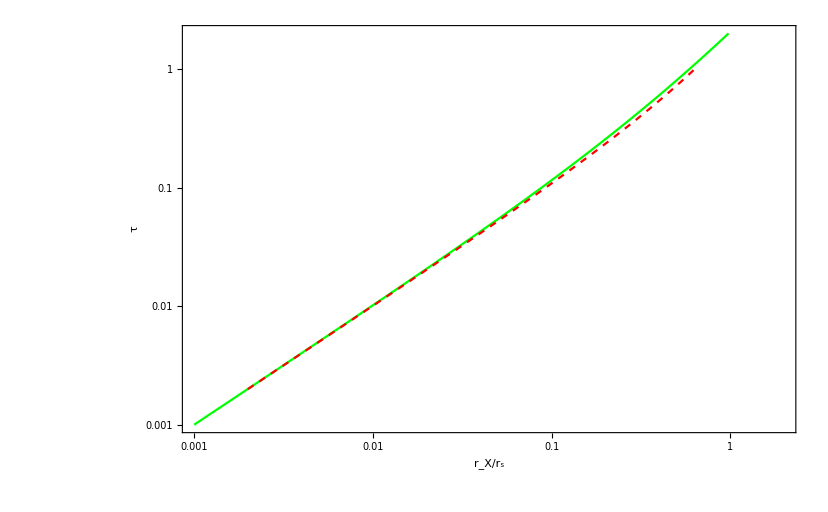

```mathematica
ListLogLogPlot[{τTab,tautab },PlotRange->{{0.001,2},{0.001,2}},Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, s],τ},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Green,{Red,Dashed}}]
```

## Try a pseudo-jaffe profile

FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

x_max= 1.1352/rt/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

M_(1/2) = (4 (-1+1/(1+1.31683/rt)+ArcTan[1.31683/rt]))/(-2+π)/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

dv_max^2/dr(r_max) = 0.387994 rt^2 ((1.1352 (1+(1.1352 (3+1.28868/rt^2+1.1352/rt))/rt))/((1+1.28868/rt^2) (1+1.1352/rt)^2 rt)-ArcTan[1.1352/rt])/.FindRoot[{(-1+1/(1+Y)+ArcTan[Y]/.Y→1.31683/rt)==1/4 (-2+π),(((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X→1.1352/rt)==0},{{rt,1.1352,0,150 1.1352}},MaxIterations→1000,AccuracyGoal→8]

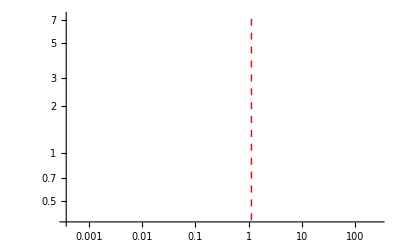

```mathematica
rmax =1.1352;
α=1.16;
rh=α*rmax;
Solh2 = Solrt[rh,rmax,rmax]
Print["x_max= ", rmax/rt /. Solh2]
Print["M_(1/2) = ",(-1+1/(1+Y)+ArcTan[Y])/(1/4 (-2+π))/.Y-> rh/rt/.Solh2]

Print["dv_max^2/dr(r_max) = ",((X (1+X (3+X+X^2)))/((1+X)^2 (1+X^2))-ArcTan[X])/(2 X^2)/.X-> rmax/rt/.Solh2]
lineStyle={Thick,Red,Dashed};
line1=Line[{{Log[rmax],Log[10^-10]},{Log[rmax],Log[3000]}}];
LogLogPlot[1/X 1/2 (-1+1/(1+X)+ArcTan[X])/.X-> r/rt/. Solh2,{r,0.001,100},Epilog->{Directive[lineStyle],line1}]
```

## Now for the Burkert profile

### Compute half-mass

```mathematica
mhalf=FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x^2/((1+x)(1+x^2))(τ^2/(τ^2+x^2)),{x,0,X}]]]
```

(τ^2 (-2 (1+τ^2) ArcTan[X]-2 Log[1+X]+Log[1+X^2]+τ (4 ArcTan[X/τ]+τ (2 Log[1+X]+Log[1+X^2]+4 Log[τ]-2 Log[X^2+τ^2]))))/(4 (-1+τ^4))

### Compute total mass

```mathematica
mtot=FullSimplify[Assuming[{τ,X} ∈Reals && τ >1&&X>0,Integrate[x^2/((1+x)(1+x^2))(τ^2/(τ^2+x^2)),{x,0,Infinity}]]]
```

(τ^2 (-π (-1+τ)^2+4 τ^2 Log[τ]))/(4 (-1+τ^4))

### Plot the 2 cases for an examples

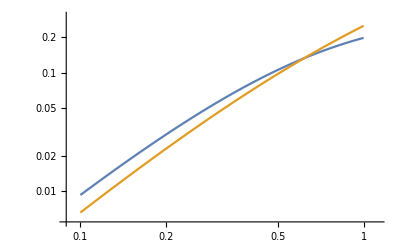

```mathematica
LogLogPlot[{2*mhalf/.X->1.1,mtot},{τ,0.1,1}]
```

### Ok they intersect, find solution numerically

```mathematica
tauSolB[Xh_]:=FindRoot[(2mhalf/.X-> Xh)==mtot,{τ,0.4 Xh^2.5}]
```

### Make a table of solutions

```mathematica
τTabB = Table[{X,tauSolB[X][[1,2]]},{X,0.5,3,0.01}];
```

#### Plot it

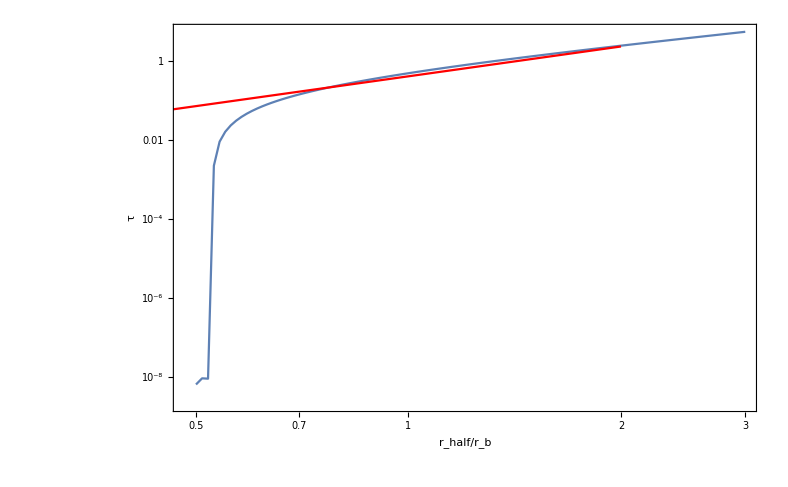

```mathematica
Show[ListLogLogPlot[τTabB,Joined-> True,Frame->True,FrameLabel-> {Subscript[r, half]/Subscript[r, b],τ},LabelStyle->Directive[Bold, Medium,25],PlotRange->Full],LogLogPlot[0.4 x^2.5,{x,0.01,2},PlotStyle->Red]]
```

#### Do the vmax constraints

```mathematica
FullSimplify[Assuming[{X,τ} ∈Reals && X>0 && τ>0,Difvmax = D[1/X mhalf,X]]];
```

```mathematica
TabtauB[τh_]:= FindRoot[Difvmax/.τ-> τh,{X,1.4 τh^0.46}]
```

### Make a table of solutions

```mathematica
XmaxTabB = Table[{τ,TabtauB[τ][[1,2]]},{τ,.01,3,0.02}];
```

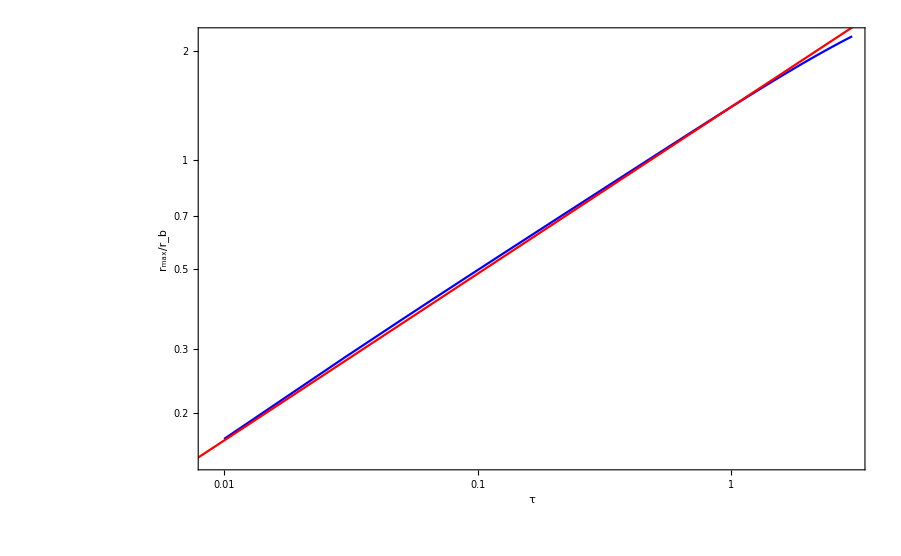

```mathematica
Show[ListLogLogPlot[{XmaxTabB},Joined-> True,Frame->True,PlotRange->Full,FrameLabel-> {τ,Subscript[r, max]/Subscript[r, b]},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Blue}],LogLogPlot[1.4 x^0.46,{x,0.001,3},PlotStyle->Red]]
```

```mathematica
tautabB = Table[{XmaxTabB[[i,2]],XmaxTabB[[i,1]]},{i,2,Length[XmaxTabB]}];
```

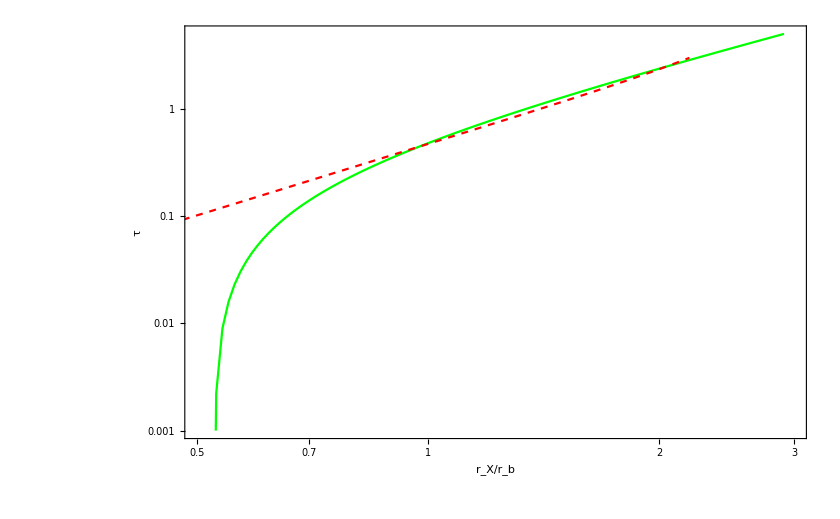

```mathematica
ListLogLogPlot[{τTabB,tautabB },PlotRange->{{0.5,3},{0.001,5}},Joined-> True,Frame->True,FrameLabel-> {Subscript[r, X]/Subscript[r, b],τ},LabelStyle->Directive[Bold, Medium,25],PlotStyle->{Green,{Red,Dashed}}]
```

```mathematica
tautabB
```

{{0.285629,0.03},{0.361898,0.05},{0.422299,0.07},{0.473579,0.09},{0.518779,0.11},{0.559574,0.13},{0.596996,0.15},{0.631731,0.17},{0.664265,0.19},{0.694953,0.21},{0.724065,0.23},{0.751811,0.25},{0.778359,0.27},{0.803844,0.29},{0.828379,0.31},{0.852056,0.33},{0.874955,0.35},{0.897144,0.37},{0.918679,0.39},{0.939611,0.41},{0.959986,0.43},{0.97984,0.45},{0.999209,0.47},{1.01812,0.49},{1.03661,0.51},{1.0547,0.53},{1.0724,0.55},{1.08974,0.57},{1.10675,0.59},{1.12342,0.61},{1.13979,0.63},{1.15586,0.65},{1.17166,0.67},{1.18718,0.69},{1.20244,0.71},{1.21745,0.73},{1.23222,0.75},{1.24677,0.77},{1.26109,0.79},{1.27519,0.81},{1.2891,0.83},{1.3028,0.85},{1.31631,0.87},{1.32963,0.89},{1.34277,0.91},{1.35574,0.93},{1.36853,0.95},{1.38116,0.97},{1.39363,0.99},{1.40594,1.01},{1.41811,1.03},{1.43012,1.05},{1.44199,1.07},{1.45371,1.09},{1.46531,1.11},{1.47676,1.13},{1.48809,1.15},{1.49929,1.17},{1.51036,1.19},{1.52131,1.21},{1.53215,1.23},{1.54287,1.25},{1.55347,1.27},{1.56396,1.29},{1.57434,1.31},{1.58462,1.33},{1.59479,1.35},{1.60485,1.37},{1.61482,1.39},{1.62468,1.41},{1.63445,1.43},{1.64413,1.45},{1.65371,1.47},{1.6632,1.49},{1.67259,1.51},{1.6819,1.53},{1.69113,1.55},{1.70026,1.57},{1.70931,1.59},{1.71828,1.61},{1.72717,1.63},{1.73598,1.65},{1.74471,1.67},{1.75336,1.69},{1.76193,1.71},{1.77043,1.73},{1.77885,1.75},{1.7872,1.77},{1.79548,1.79},{1.80369,1.81},{1.81183,1.83},{1.8199,1.85},{1.8279,1.87},{1.83583,1.89},{1.8437,1.91},{1.8515,1.93},{1.85924,1.95},{1.86692,1.97},{1.87453,1.99},{1.88208,2.01},{1.88957,2.03},{1.897,2.05},{1.90437,2.07},{1.91168,2.09},{1.91894,2.11},{1.92613,2.13},{1.93327,2.15},{1.94036,2.17},{1.94739,2.19},{1.95436,2.21},{1.96128,2.23},{1.96815,2.25},{1.97497,2.27},{1.98173,2.29},{1.98844,2.31},{1.9951,2.33},{2.00172,2.35},{2.00828,2.37},{2.01479,2.39},{2.02126,2.41},{2.02767,2.43},{2.03404,2.45},{2.04036,2.47},{2.04664,2.49},{2.05287,2.51},{2.05906,2.53},{2.0652,2.55},{2.07129,2.57},{2.07735,2.59},{2.08335,2.61},{2.08932,2.63},{2.09524,2.65},{2.10112,2.67},{2.10696,2.69},{2.11276,2.71},{2.11852,2.73},{2.12424,2.75},{2.12991,2.77},{2.13555,2.79},{2.14115,2.81},{2.14671,2.83},{2.15223,2.85},{2.15771,2.87},{2.16316,2.89},{2.16856,2.91},{2.17394,2.93},{2.17927,2.95},{2.18457,2.97},{2.18983,2.99}}

```mathematica
1.42/1.476762588
```

0.961563

```mathematica
1.4100000000000001/1.47
```

0.959184

```mathematica
τTabB
```

{{0.5,6.65608×10^-9},{0.51,9.51041×10^-9},{0.52,9.32803×10^-9},{0.53,0.00221856},{0.54,0.00896749},{0.55,0.0159213},{0.56,0.0230596},{0.57,0.0303714},{0.58,0.0378499},{0.59,0.0454897},{0.6,0.053287},{0.61,0.0612386},{0.62,0.0693418},{0.63,0.0775944},{0.64,0.0859945},{0.65,0.0945403},{0.66,0.10323},{0.67,0.112063},{0.68,0.121038},{0.69,0.130153},{0.7,0.139408},{0.71,0.148801},{0.72,0.158331},{0.73,0.167998},{0.74,0.177802},{0.75,0.18774},{0.76,0.197812},{0.77,0.208019},{0.78,0.218358},{0.79,0.22883},{0.8,0.239434},{0.81,0.250169},{0.82,0.261034},{0.83,0.27203},{0.84,0.283155},{0.85,0.294409},{0.86,0.305792},{0.87,0.317303},{0.88,0.328942},{0.89,0.340708},{0.9,0.3526},{0.91,0.364619},{0.92,0.376764},{0.93,0.389034},{0.94,0.40143},{0.95,0.41395},{0.96,0.426594},{0.97,0.439363},{0.98,0.452255},{0.99,0.46527},{1.,0.478408},{1.01,0.491668},{1.02,0.505051},{1.03,0.518555},{1.04,0.532181},{1.05,0.545928},{1.06,0.559796},{1.07,0.573785},{1.08,0.587894},{1.09,0.602123},{1.1,0.616471},{1.11,0.630939},{1.12,0.645526},{1.13,0.660232},{1.14,0.675056},{1.15,0.689999},{1.16,0.705059},{1.17,0.720238},{1.18,0.735533},{1.19,0.750946},{1.2,0.766476},{1.21,0.782123},{1.22,0.797886},{1.23,0.813765},{1.24,0.829761},{1.25,0.845872},{1.26,0.862098},{1.27,0.87844},{1.28,0.894897},{1.29,0.911469},{1.3,0.928155},{1.31,0.944956},{1.32,0.961871},{1.33,0.9789},{1.34,0.996043},{1.35,1.0133},{1.36,1.03067},{1.37,1.04815},{1.38,1.06575},{1.39,1.08346},{1.4,1.10128},{1.41,1.11921},{1.42,1.13726},{1.43,1.15541},{1.44,1.17368},{1.45,1.19206},{1.46,1.21056},{1.47,1.22916},{1.48,1.24788},{1.49,1.2667},{1.5,1.28564},{1.51,1.30469},{1.52,1.32385},{1.53,1.34311},{1.54,1.36249},{1.55,1.38198},{1.56,1.40158},{1.57,1.42129},{1.58,1.4411},{1.59,1.46103},{1.6,1.48107},{1.61,1.50121},{1.62,1.52146},{1.63,1.54183},{1.64,1.5623},{1.65,1.58288},{1.66,1.60357},{1.67,1.62436},{1.68,1.64527},{1.69,1.66628},{1.7,1.6874},{1.71,1.70863},{1.72,1.72996},{1.73,1.7514},{1.74,1.77295},{1.75,1.79461},{1.76,1.81637},{1.77,1.83825},{1.78,1.86022},{1.79,1.88231},{1.8,1.9045},{1.81,1.92679},{1.82,1.9492},{1.83,1.97171},{1.84,1.99432},{1.85,2.01705},{1.86,2.03987},{1.87,2.06281},{1.88,2.08584},{1.89,2.10899},{1.9,2.13224},{1.91,2.15559},{1.92,2.17905},{1.93,2.20262},{1.94,2.22629},{1.95,2.25006},{1.96,2.27394},{1.97,2.29793},{1.98,2.32202},{1.99,2.34621},{2.,2.37051},{2.01,2.39491},{2.02,2.41942},{2.03,2.44403},{2.04,2.46874},{2.05,2.49356},{2.06,2.51848},{2.07,2.54351},{2.08,2.56864},{2.09,2.59387},{2.1,2.61921},{2.11,2.64465},{2.12,2.67019},{2.13,2.69584},{2.14,2.72159},{2.15,2.74744},{2.16,2.7734},{2.17,2.79946},{2.18,2.82562},{2.19,2.85188},{2.2,2.87825},{2.21,2.90472},{2.22,2.93129},{2.23,2.95796},{2.24,2.98474},{2.25,3.01162},{2.26,3.0386},{2.27,3.06568},{2.28,3.09287},{2.29,3.12015},{2.3,3.14754},{2.31,3.17503},{2.32,3.20263},{2.33,3.23032},{2.34,3.25812},{2.35,3.28601},{2.36,3.31401},{2.37,3.34211},{2.38,3.37031},{2.39,3.39862},{2.4,3.42702},{2.41,3.45553},{2.42,3.48413},{2.43,3.51284},{2.44,3.54165},{2.45,3.57056},{2.46,3.59957},{2.47,3.62868},{2.48,3.65789},{2.49,3.6872},{2.5,3.71661},{2.51,3.74613},{2.52,3.77574},{2.53,3.80545},{2.54,3.83527},{2.55,3.86518},{2.56,3.8952},{2.57,3.92531},{2.58,3.95553},{2.59,3.98584},{2.6,4.01626},{2.61,4.04678},{2.62,4.07739},{2.63,4.10811},{2.64,4.13892},{2.65,4.16983},{2.66,4.20085},{2.67,4.23196},{2.68,4.26318},{2.69,4.29449},{2.7,4.3259},{2.71,4.35741},{2.72,4.38903},{2.73,4.42074},{2.74,4.45255},{2.75,4.48446},{2.76,4.51646},{2.77,4.54857},{2.78,4.58078},{2.79,4.61309},{2.8,4.64549},{2.81,4.67799},{2.82,4.7106},{2.83,4.7433},{2.84,4.7761},{2.85,4.809},{2.86,4.842},{2.87,4.87509},{2.88,4.90829},{2.89,4.94158},{2.9,4.97498},{2.91,5.00847},{2.92,5.04206},{2.93,5.07575},{2.94,5.10953},{2.95,5.14342},{2.96,5.1774},{2.97,5.21148},{2.98,5.24566},{2.99,5.27994},{3.,5.31432}}